```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin active addresses: https://bitinfocharts.com/comparison/activeaddresses-btc.html#log&alltime.

- Bitcoin market capitalization: https://bitinfocharts.com/comparison/bitcoin-marketcap.html#log&alltime.

## Outline

The main idea is to fit a curve to the number of active Bitcoin users (represented by active Bitcoin addresses), and then use that smoothed curve to fit Bitcoin’s value (represented by its Market capitalization), using a generalized Metcalfe’s law model.
Then we can see if Bitcoin’s market cap growth is in line with the growth in the number of its active users, according to Metcalfe’s law.
There are other applications in the paper that are out of scope / unimplemented for now (LPPLS model).

```mathematica
(* 1. Active users (active addresses proxy) *)
(* 1.1 Obtain the data. From https://bitinfocharts.com: Number of unique (from or to) addresses per day *)
base=DirectoryName[NotebookFileName[]];
first = "2010-07-17"
last=DateString[Yesterday,"ISODate"]
```

2010-07-17

2026-08-05

```mathematica
(* TODO: Incorporate Lightning network activity *)
activeAddressesImport=Import["https://bitinfocharts.com/comparison/activeaddresses-btc.html#log&alltime", "text"];
activeAddressesCase=StringCases[activeAddressesImport, RegularExpression["\[\[new Date.*\]\]"]][[1]];
activeAddressesReplace=StringReplace[activeAddressesCase, {"new Date(\""-> "", "\")"-> "", "],"-> "\n", "["-> "", "]"-> ""}];

activeAddressesSplit=StringSplit[activeAddressesReplace, "\n"];
```

```mathematica
hDailyListFull={#[[1]],ToExpression[#[[2]]]}&/@(StringSplit[#,","]&/@activeAddressesSplit)
```

```mathematica
firstDate=StringReplace[first, "-"-> "/"];
hDailyList=Select[hDailyListFull, LexicographicOrder[firstDate,#[[1]]]>=0&]
```

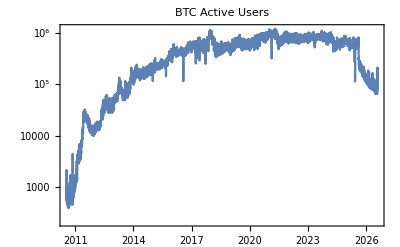

```mathematica
DateListLogPlot[hDailyList, PlotLabel->"BTC Active Users"]
```

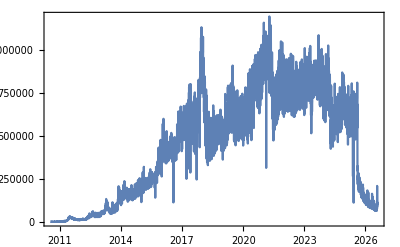

```mathematica
DateListPlot[hDailyList]
```

```mathematica
hDailyList[[1]][[1]]
```

2010/07/17

```mathematica
hDailyListFiltered=Select[hDailyList, NumberQ[#[[2]]]&]
```

```mathematica
Length /@{hDailyList, hDailyListFiltered}
```

{5865,5841}

```mathematica
(* Cap address activity data to avoid downtrend: *)
maxCapDate=MaximalBy[hDailyListFiltered, Last]//First//First
```

2021/04/15

```mathematica
hDailyListCapped = Select[hDailyList,AlphabeticOrder[#[[1]],maxCapDate]==1&];
```

```mathematica
hDailyListCapped//Length
```

3925

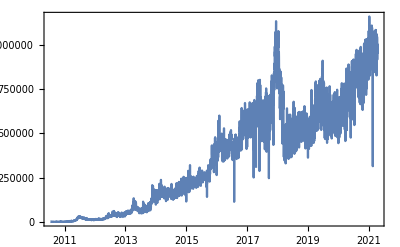

```mathematica
DateListPlot[hDailyListCapped]
```

```mathematica
dailyList={DayCount[first, #[[1]]],#[[2]]}& /@hDailyListCapped
```

```mathematica
activeUsers=Select[dailyList,NumberQ[#[[2]]]&]
```

```mathematica
activeUsersLog={#[[1]],Log[N[#[[2]]]]}&/@activeUsers
```

```mathematica
(* 2. Market cap data: *)
marketCapImport=Import["https://bitinfocharts.com/comparison/bitcoin-marketcap.html#log&alltime", "text"];
marketCapCase=StringCases[marketCapImport, RegularExpression["\[\[new Date.*\]\]"]][[1]];
marketCapReplace=StringReplace[marketCapCase, {"new Date(\""-> "", "\")"-> "", "],"-> "\n", "["-> "", "]"-> ""}];
marketCapSplit=StringSplit[marketCapReplace, "\n"];
```

```mathematica
(* 2.1 Obtain market cap data for the period: *)
marketCap={#[[1]],ToExpression[#[[2]]]}&/@(StringSplit[#,","]&/@marketCapSplit)
```

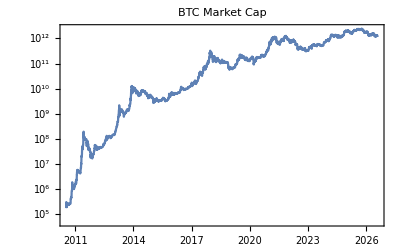

```mathematica
DateListLogPlot[marketCap, PlotLabel->"BTC Market Cap"]
```

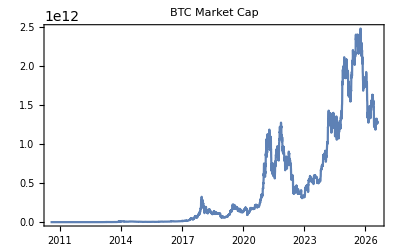

```mathematica
DateListPlot[marketCap, PlotLabel->"BTC Market Cap"]
```

```mathematica
marketCap2={DayCount[first, #[[1]]],#[[2]]}& /@marketCap
```

```mathematica
marketCapLog={#[[1]],Log[N[#[[2]]]]}&/@marketCap2
```

```mathematica
(* Now, do a fit for Metcalfe's law up to latest data: *)
days=DayCount[last, first]
```

5863

```mathematica
(* Non linear fit of the users: *)
{a,b,c}=.;
modelUsers=a+b Log[c +x];
fitUsers=FindFit[activeUsersLog, modelUsers,{a,b,c}, x]
```

{a→-3.97366,b→2.16211,c→74.4435}

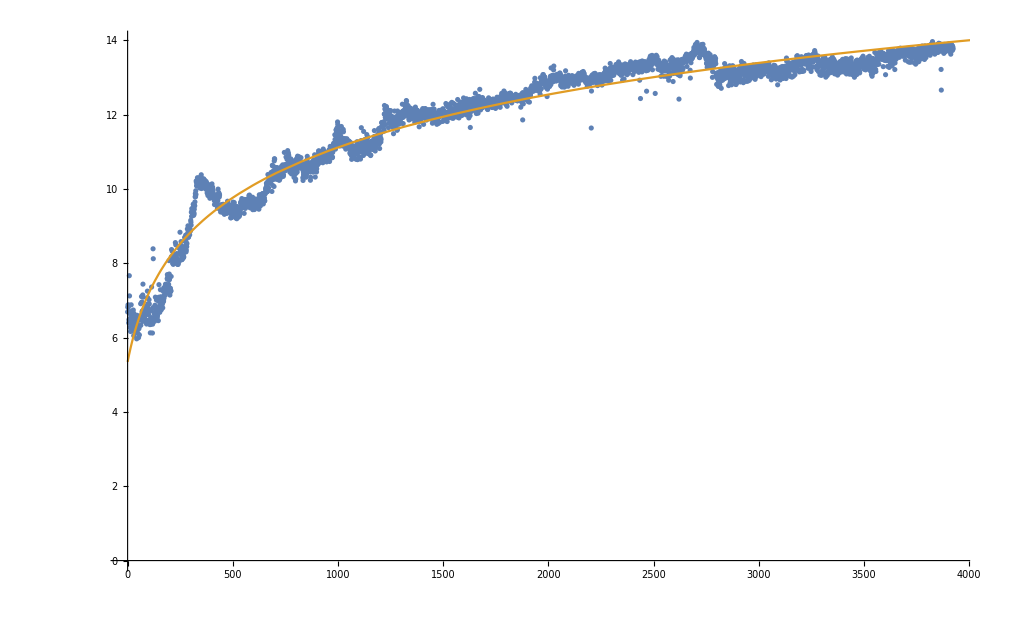

```mathematica
Show[ListPlot[activeUsersLog], Plot[{Orange, modelUsers/.fitUsers}, {x, 0, days}]]
```

```mathematica
(* Non-parametric fit of the users: *)
Export[base<>"csv/activeUsersLog.tsv", Join[{{"time","value"}},activeUsersLog]]
```

/Users/mauro/Projects/Bitcoin/csv/activeUsersLog.tsv

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
maxDist=Max[activeUsersLog[[All, 1]]]-Min[activeUsersLog[[All, 1]]];
```

```mathematica
usersSpan=0.33 (* From R. TODO: Automate *)
```

0.33

```mathematica
npFitUsers = LoessR[activeUsersLog, Scaled[usersSpan], activeUsersLog[[All, 1]]];
```

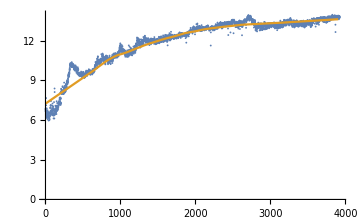

```mathematica
Show[ListPlot[activeUsersLog, ImageSize->Medium],   ListLinePlot[{{0,0},npFitUsers}]]
```

```mathematica
(* Log function of the users *)
modelUsers
fitUsers
```

a+b Log[c+x]

{a→-3.97366,b→2.16211,c→74.4435}

```mathematica
logu[days_]:= modelUsers/.fitUsers/.x-> days
logu[i]
logu[0]
```

-3.97366+2.16211 Log[74.4435+i]

5.34513

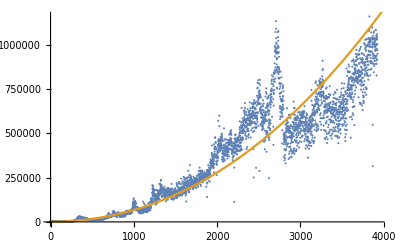

```mathematica
Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@activeUsersLog],Plot[{Orange,Exp[logu[x]]}, {x, 0, days},Evaluated-> True]]
```

```mathematica
(* Non-parametric function of the users *)
npFitUsersInterpolated:= Interpolation[npFitUsers]
loguNp[days_]:= npFitUsersInterpolated[days]
```

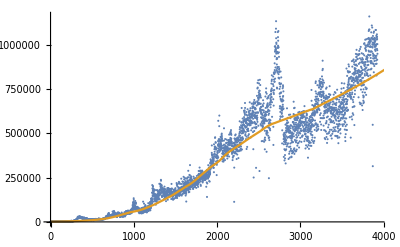

```mathematica
Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@activeUsersLog],Plot[{Orange,Exp[loguNp[x]]}, {x, 1, days},{Evaluated-> True}]]
```

```mathematica
(* Non linear fit of the market cap (Metcalfe): *)
logu[x]
```

-3.97366+2.16211 Log[74.4435+x]

```mathematica
logModelMetcalfe=α+β logu[x];
fitMetcalfe=FindFit[marketCapLog,logModelMetcalfe,{α,β},x]
```

{α→-2.06146,β→2.04022}

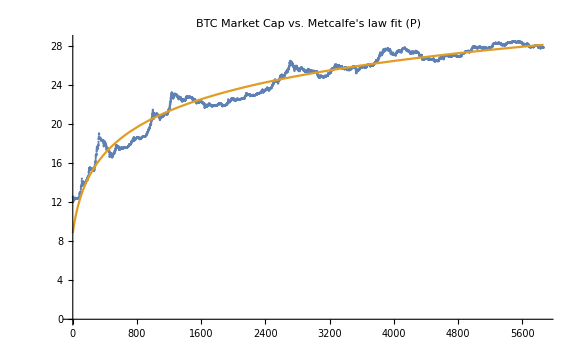

```mathematica
bitcoinMarketCapVsMetcalfe =Show[ListPlot[marketCapLog], Plot[{Orange, logModelMetcalfe/.fitMetcalfe}, {x, 0, days}], PlotLabel-> "BTC Market Cap vs. Metcalfe's law fit (P)", ImageSize-> Large]
```

```mathematica
Export[base<>"pdf/BTC_MarketCap_vs_Metcalfe.pdf", bitcoinMarketCapVsMetcalfe]
```

/Users/mauro/Projects/Bitcoin/pdf/BTC_MarketCap_vs_Metcalfe.pdf

```mathematica
(* Non linear fit of the market cap (Metcalfe) using the non-parametric function of the users: *)
logModelMetcalfeNp=α+β loguNp[x];
fitMetcalfeNp=FindFit[marketCapLog[[2;;-21]],logModelMetcalfeNp,{α,β},x]
```

InterpolatingFunction::dmval: Input value {3904.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3905.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3906.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{α→-2.97067,β→2.14304}

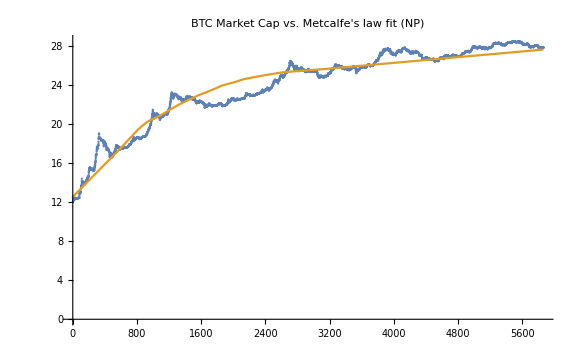

```mathematica
bitcoinMarketCapVsMetcalfeNp =Show[ListPlot[marketCapLog], Plot[{Orange, logModelMetcalfeNp/.fitMetcalfeNp}, {x, 1, days}], PlotLabel-> "BTC Market Cap vs. Metcalfe's law fit (NP)", ImageSize-> Large]
```

```mathematica
Export[base<>"pdf/BTC_MarketCap_vs_Metcalfe-NpUsers.pdf", bitcoinMarketCapVsMetcalfeNp]
```

/Users/mauro/Projects/Bitcoin/pdf/BTC_MarketCap_vs_Metcalfe-NpUsers.pdf

```mathematica
(* Log function of the market cap *)
logModelMetcalfe
fitMetcalfe
```

α+β (-3.97366+2.16211 Log[74.4435+x])

{α→-2.06146,β→2.04022}

```mathematica
logp[i_]:= logModelMetcalfe/.fitMetcalfe/.x-> i
logp[i]
logp[0]
```

-2.06146+2.04022 (-3.97366+2.16211 Log[74.4435+i])

8.84378

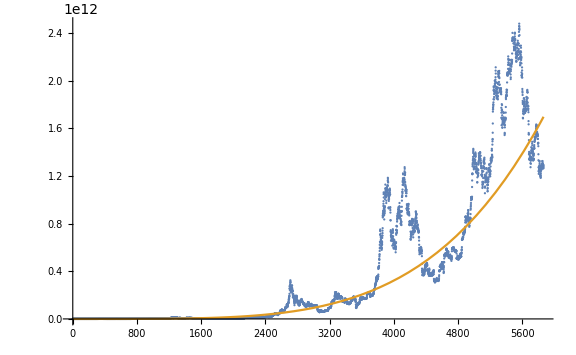

```mathematica
Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@ marketCapLog, ImageSize->Large],Plot[{Orange,Exp[logp[x]]}, {x, 0, days}, Evaluated-> True]]
```

```mathematica
(* Log function of the market cap, non-parametric users *)
logModelMetcalfeNp
fitMetcalfeNp
```

α+β InterpolatingFunction[…][x]

{α→-2.97067,β→2.14304}

```mathematica
logpNp[i_]:= logModelMetcalfeNp/.fitMetcalfeNp/.x-> i
logp[i]
logp[0]
```

-2.06146+2.04022 (-3.97366+2.16211 Log[74.4435+i])

8.84378

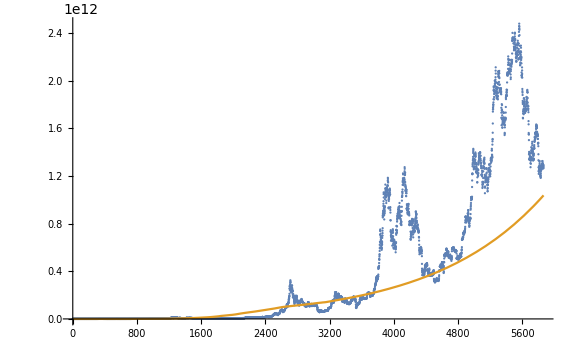

```mathematica
Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@ marketCapLog, ImageSize->Large],Plot[{Orange,Exp[logpNp[x]]}, {x, 1, days}, Evaluated-> True]]
```

```mathematica
(* Bicoin overvaluation *)
marketCapLog[[-1]]
```

{5863,27.8871}

```mathematica
marketCap[[-1]]
```

{2026/08/05,1291912249114}

```mathematica
Exp[marketCapLog[[-1]][[2]]]/Exp[logp[marketCapLog[[-1]][[1]]]]
```

0.760963

```mathematica
(* latest closing price [USD] (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) *)
(* Automated download: *)
timeStartTs=UnixTime[last];
timeEndTs=timeStartTs+86400;
latestPriceUrl="https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart="<>ToString[timeStartTs]<>"&timeEnd="<>ToString[timeEndTs]<>"&interval=1d"
```

https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart=1785880800&timeEnd=1785967200&interval=1d

```mathematica
latestPriceData=Import[latestPriceUrl]
```

```mathematica
latestPrice=Flatten[latestPriceData[[1]][[2]][[5]][[2]]][[-1]][[2]][[5]][[2]]
```

64597.5

```mathematica
(* Estimated price for the current (last) date: *)
estimatedPrice=latestPrice/(Exp[marketCapLog[[-1]][[2]]]/Exp[logp[marketCapLog[[-1]][[1]]]])
```

84889.1

```mathematica
(* Overvaluation percentage: *)
latestPrice/estimatedPrice
Print["Current overvaluation (P): ", NumberForm[(latestPrice/estimatedPrice-1)100,{4,2}], "%"]
```

0.760963

Current overvaluation (P): -23.90%

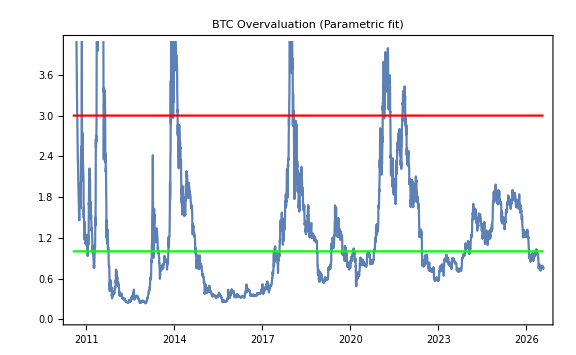

```mathematica
(* Overvaluations: *)
bitcoinOvervaluation=DateListPlot[{#[[1]], Exp[#[[2]]]/Exp[logp[#[[1]] ]]}&/@marketCapLog, DateFunction:> (DatePlus[first, #]&),PlotLabel->"BTC Overvaluation (Parametric fit)", ImageSize->Large];
bitcoinOvervaluation = Show[bitcoinOvervaluation,DateListPlot[{#[[1]],1}&/@marketCapLog,ColorFunction->Function[x, Green],DateFunction:>(DatePlus[first, #]&)],DateListPlot[{#[[1]],3}&/@marketCapLog,ColorFunction->Function[x, Red],DateFunction:>(DatePlus[first, #]&)], ImageSize->Large]
```

```mathematica
Export[base <>"pdf/BTC_Overvaluation_"<>last<>".pdf", bitcoinOvervaluation]
```

/Users/mauro/Projects/Bitcoin/pdf/BTC_Overvaluation_2026-08-05.pdf

```mathematica
(* Export prediction: *)
Get[base<>"PredictionsExport.wl"];
```

```mathematica
exportPrediction[bitcoinOvervaluation,"BTC_Overvaluation-P",last];
```

CreateDirectory::eexist: /Users/mauro/Projects/Bitcoin/predictions already exists.

```mathematica
(* Bicoin overvaluation (non-parametric users) *)
marketCapLog[[-1]]
```

{5863,27.8871}

```mathematica
marketCap[[-1]]
```

{2026/08/05,1291912249114}

```mathematica
Exp[marketCapLog[[-1]][[2]]]/Exp[logpNp[marketCapLog[[-1]][[1]]]]
```

InterpolatingFunction::dmval: Input value {5863} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.245

```mathematica
(* Estimated price for the current (last) date: *)
estimatedPriceNp=latestPrice/(Exp[marketCapLog[[-1]][[2]]]/Exp[logpNp[marketCapLog[[-1]][[1]]]])
```

InterpolatingFunction::dmval: Input value {5863} lies outside the range of data in the interpolating function. Extrapolation will be used.

51885.6

```mathematica
(* Overvaluation percentage: *)
Print["Current overvaluation (NP): ", NumberForm[(latestPrice/estimatedPriceNp-1)100,{4,2}], "%"]
```

Current overvaluation (NP): 24.50%

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3904} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3905} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

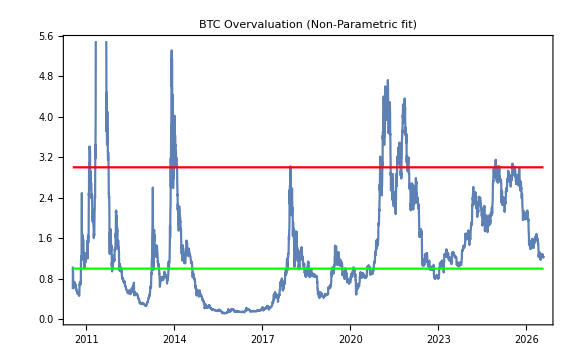

```mathematica
(* Overvaluations: *)
bitcoinOvervaluationNp=DateListPlot[{#[[1]], Exp[#[[2]]]/Exp[logpNp[#[[1]] ]]}&/@marketCapLog, DateFunction:> (DatePlus[first, #]&),PlotLabel->"BTC Overvaluation (Non-Parametric fit)", ImageSize->Large];
bitcoinOvervaluationNp = Show[bitcoinOvervaluationNp,DateListPlot[{#[[1]],1}&/@marketCapLog,ColorFunction->Function[x, Green],DateFunction:>(DatePlus[first, #]&)],DateListPlot[{#[[1]],3}&/@marketCapLog,ColorFunction->Function[x, Red],DateFunction:>(DatePlus[first, #]&)], ImageSize->Large]
```

```mathematica
Export[base <>"pdf/BTC_Overvaluation-NP_"<>last<>".pdf", bitcoinOvervaluationNp]
```

/Users/mauro/Projects/Bitcoin/pdf/BTC_Overvaluation-NP_2026-08-05.pdf

```mathematica
(* Export prediction: *)
exportPrediction[bitcoinOvervaluationNp,"BTC_Overvaluation-NP",last];
```

CreateDirectory::eexist: /Users/mauro/Projects/Bitcoin/predictions already exists.

```mathematica
estimatedPriceMean=Mean[{estimatedPrice, estimatedPriceNp}]
```

68387.4